Classification with San Francisco Crime Data Set
Course Name: ACM40730 Mathematica for Research
Name: Edward Donlon      Student Number: 17206010
Date: Friday 1st December 2017

## Introduction

The aim of this project is to examine the San Francisco Police Department Crime Incidents for 2017 Data Set and then to demonstrate machine learning in Mathematica by using the Classifier function to predict crimes. In the data set there are 13 columns, namely:

IncidntNum: Internal code assigned to crime by police department.

Category: The type of crime that was committed (39 different categories). This is the variable that we are going to try to predict.

Description: A brief explanation of the crime committed.

DayOfWeek.

Date: MM/DD/YYYY format.

Time:  24 hour format.

PdDistrict: District where the crime occurred (10 different districts).

Resolution: Outcome of the crime e.g. arrested/ prosecuted for lesser offence etc. (15 different resolutions).

Address: Approximate street address of the crime.

X: Longitude.

Y: Latitude.

PdId: Unique 14 digit identifier for each crime.

## Import Data

DataSF is an initiative that provides freely available data sets about services provided in San Francisco, with the goal of improving public operations through smarter use of data. The Police Department Incidents data can be obtained as a CSV through the public safety section from https://datasf.org/opendata/.

```mathematica
SetDirectory["C:/Users/Edward/Documents/Wolfram Mathematica/Project"];
filename="Police_Department_Incidents-2017.csv";
```

The SemanticImport function is very useful for importing csv data, as it intuitively formats Dates and Times in the correct way, inserts an appropriate header line and outputs the data in a Dataset.

```mathematica
ds=SemanticImport[filename]
```

Dataset[<>]

#### Data Cleaning

Before doing any sort of analysis, it is important to search through the dataset for any missing values. This can be done in Mathematica using the MissingQ function.

```mathematica
MissingQ[ds]
```

False

This is quite good news, as missing data values usually cause problems in data analysis. However, we may still have some incorrect values entered in the data set, so we will have to be vigilant to check for these.

#### Preliminary analysis:

```mathematica
ds // Dimensions
```

{129202,13}

Our data set contains 129202 total incidents.

```mathematica
Length[Union[ds[All, "Category"]]]
Length[Union[ds[All, "PdDistrict"]]]
```

39

10

Confirming we have all 39 different crime categories and 10 Police Department districts.

Our data ranges from the 1st of January 2017 to the 5th of November 2017:

```mathematica
Sort[ds[[All,"Date"]]][[1]]
Sort[ds[[All,"Date"]]][[-1]]
```

01/01/2017

11/05/2017

Look at the most common crimes:

```mathematica
Sort[Counts[ds[[All, "Category"]]]] // Reverse
```

Dataset[<>]

## Visualisation

### Basic Statistics

We initialise some lists at the start of this section containing all of the possible crime categories, days of the week and police department districts. These will be necessary later in order to use the Manipulate function correctly.

```mathematica
categories=Normal[Union[ds[All,"Category"]]];
daysofweek = Normal[Union[ds[All,"DayOfWeek"]]];
districts=Normal[Union[ds[All, "PdDistrict"]]];
```

Now we can begin to look at the data using Bar Charts. As before, we see that “Larceny/Theft” is the most commonly occurring overall crime.

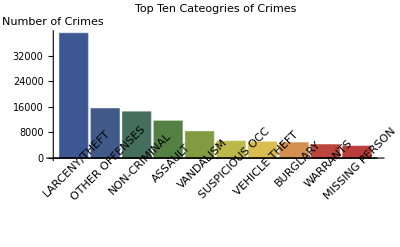

```mathematica
BarChart[Reverse[Sort[Counts[ds[[All, "Category"]]]]][[;;10]],PlotLabel->Style["Top Ten Cateogries of Crimes",FontSize->18],AxesLabel->"Number of Crimes",ImageSize->Scaled[0.6], ChartStyle->"DarkRainbow", ChartLabels->Placed[Automatic,Axis,Rotate[#,Pi/4]&]]
```

Crimes by District

We can look at the total number of crimes by police department district:

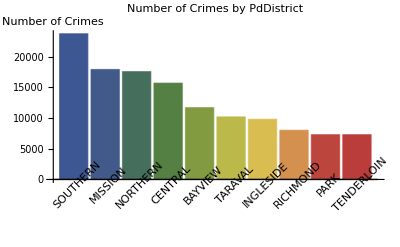

```mathematica
BarChart[Sort[Counts[ds[[All, "PdDistrict"]]]] // Reverse,PlotLabel->Style["Number of Crimes by PdDistrict",FontSize->18],AxesLabel->"Number of Crimes",ImageSize->Scaled[0.6], ChartStyle->"DarkRainbow",ChartLabels->Placed[Automatic,Axis,Rotate[#,Pi/4]&]]
```

#### Crime Dates and Day of Week

Also we can look at the total number of crimes by the day of the week on which they occur:

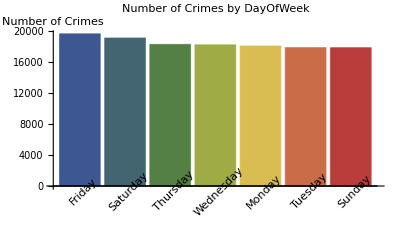

```mathematica
BarChart[Sort[Counts[ds[[All, "DayOfWeek"]]]] // Reverse,PlotLabel->Style["Number of Crimes by DayOfWeek",FontSize->18],AxesLabel->"Number of Crimes", ChartStyle->"DarkRainbow",ImageSize->Scaled[0.6],ChartLabels->Placed[Automatic,Axis,Rotate[#,Pi/4]&]]
```

As we would have expected, more crimes occur on the weekend nights of Friday and Saturday.

Using the Manipulate function, we are able to break down the different locations of crimes by their day of the week:

```mathematica
Manipulate[BarChart[Sort[Counts[Select[ds,StringContainsQ[#PdDistrict,District]&][[All, "DayOfWeek"]]]] // Reverse,PlotLabel->Style["Crime Locations by DayOfWeek",FontSize->18],AxesLabel->"Number of Crimes",ImageSize->Scaled[0.6], ChartStyle->"DarkRainbow",ChartLabels->Placed[Automatic,Axis,Rotate[#,Pi/4]&]],{District,districts}]
```

And the category of crime:

```mathematica
Manipulate[BarChart[Sort[Counts[Select[ds,StringContainsQ[#Category,crime]&][[All, "DayOfWeek"]]]] // Reverse,PlotLabel->Style["Categories of Crime by DayOfWeek",FontSize->18],AxesLabel->"Number of Crimes",ImageSize->Scaled[0.6], ChartStyle->"DarkRainbow",ChartLabels->Placed[Automatic,Axis,Rotate[#,Pi/4]&]],{crime,categories}]
```

To examine seasonality of crimes, we can use a manipulate to select categories of crime and plot the result using DateHistogram:

```mathematica
Manipulate[DateHistogram[Select[ds,StringContainsQ[#Category,crime]&][[All,"Date"]],"Month",ImageSize->Scaled[0.6],PlotLabel->"Monthly breakdown of Crime by Category"], {crime,categories}]
```

#### Time of Crime

Using a similar approach, we can also plot the times of the day that each crime occurs:

```mathematica
Manipulate[DateHistogram[Select[ds,StringContainsQ[#Category,crime]&][[All,"Time"]],"Hour",ImageSize->Scaled[0.6],PlotLabel->"Time of Day of Crimes by Category",Ticks->Automatic], {crime,categories}]
```

### Geospatial Data

#### Mapping Basics

Mathematica has access to lots of information regarding geographical locations. For example, for the city of San Francisco we can find out it’s current population, weather, time zone, and more.

```mathematica
SFdata = CityData[{"SanFrancisco", "California", "UnitedStates"}]
```

San Francisco

```mathematica
SFdata["Population"]
```

870887 people

We can use the location coordinates given to us to plot the location of San Francisco on a map of the USA.

```mathematica
Graphics[{EdgeForm[Black],LightGray,CountryData["UnitedStates","Polygon"],Blue,PointSize[0.02],Tooltip[Point[Reverse[SFdata["Coordinates"]]],"San Francisco"]},PlotLabel->"Location of San Francisco in the USA"]
```

-Graphics-

DynamicGeoGraphics can be used to create an interactive map of the city of San Francisco.

```mathematica
DynamicGeoGraphics[{Polygon[LinguisticAssistant]}]
```

### Mapping Crime

#### Police Districts

To plot the crimes on map, the latitude-longitude pairs in the data set need to be transformed into the correct projection method used by the map. The Point and GeoPosition functions here do this for us once we extract the values of the coordinates in the correct format from our dataset.

```mathematica
GeoGraphics[Point@GeoPosition@Normal[Values[ds[[All,{"Y","X"}]]]],GeoRange->Automatic,PlotLabel->"All 2017 Crimes in San Francisco",ImageSize->Large]
```

-Graphics-

If we wish to see each police department district on one map, colouring each set of coordinate points by its district would allow us to see it more clearly. To do this, we’ll create a helper function plotDistrict that selects all of the relevant sets of coordinate points for a particular district and plots them with a distinct colour.

```mathematica
colors=ColorData[1,"ColorList"];
```

```mathematica
plotDistrict[d_]:=(
(* Return a GeoGraphics object that plots the specific crimes for that region *)
GeoGraphics[{colors[[d]],Point@GeoPosition@Normal[Values[Select[ds,StringContainsQ[#PdDistrict,districts[[d]]]&][[All,{"Y","X"}]]]]}]
)
```

```mathematica
p1 = plotDistrict[1];
p2 = plotDistrict[2];
p3 = plotDistrict[3];
p4 = plotDistrict[4];
p5 = plotDistrict[5];
p6 = plotDistrict[6];
p7 = plotDistrict[7];
p8 = plotDistrict[8];
p9 = plotDistrict[9];
p10 = plotDistrict[10];
```

We can then plot all of the crimes again on one map, but now coloured by its district.

```mathematica
Show[p1, p2, p3, p4, p5, p6, p7, p8, p9, p10, ImageSize->Large, PlotLabel->"The 10 Police Department Districts of San Francisco"]
```

-Graphics-

Examine the different PdDistricts using a Manipulate:

```mathematica
Manipulate[DynamicGeoGraphics[Point@GeoPosition@(Normal[Values[Select[ds,StringContainsQ[#PdDistrict,District]&][[All,{"Y","X"}]]]]), ImageSize->Large, PlotLabel->"Districts of San Francisco"],{District,districts}]
```

#### Categories of Crime

Probably of more interest is examining where certain types of crimes occur throughout the city.

```mathematica
Manipulate[DynamicGeoGraphics[{Red,Point@GeoPosition@(Normal[Values[Select[ds,StringContainsQ[#Category,crime]&][[All,{"Y","X"}]]]])}, ImageSize->Large],{crime,categories}]
```

Viewing the data in this we, we can easily notice locations where there is a high concentration of a particular crime. For instance, if we look at the location of DRUG/NARCOTIC crimes:

```mathematica
GeoGraphics[{Red,Point@GeoPosition@(Normal[Values[Select[ds,StringContainsQ[#Category,"DRUG/NARCOTIC"]&][[All,{"Y","X"}]]]])}, PlotLabel->"Crime Locations for Drug/Narcotics"]
```

-Graphics-

We can also view this data as GeoHistogram, which shows us more clearly higher areas of crime concentration.

```mathematica
GeoHistogram[GeoPosition@Normal[Values[Select[ds,StringContainsQ[#Category,"DRUG/NARCOTIC"]&][[All,{"Y","X"}]]]],ColorFunction->"TemperatureMap", PlotLegends->Automatic,PlotLabel->"Density of Drug/Narcotics Crimes"]
```

-Graphics-

## Classification

Now we will look at using Mathematica’s Classifier function to attempt to predict the category of crime given other information regarding an incident. Classify is capable of handling many different forms of data as input and generates a ClassifierFunction that attempts to classify data based on the examples and classes given.

In order for our input to be accepted correctly, we need to create a relation in this format:

```mathematica
ds[1][[2]]->Values[ds[1][[3;;13]]]
```

WARRANTS→Dataset[<>]

Of course, not all of these variables shown above will be useful as predictor variables. To begin, we will use 5 of the most obvious features for prediction.

```mathematica
features = {"DayOfWeek","Date","Time","PdDistrict","Location"}
```

{DayOfWeek,Date,Time,PdDistrict,Location}

Unfortunately, the Classifier function doesn’t seem to perform well on large datasets. To counter this, we’ll break the dataset into a smaller one and look to classify the 10 most common categories of crime (instead of the original 39 categories in the dataset).

```mathematica
topcrimes =Commonest[ds[[All,"Category"]],10]    (* List of top ten most common crimes. *)
reducedDs=Select[ds,StringContainsQ[#Category,topcrimes]&];
```

{WARRANTS,BURGLARY,SUSPICIOUS OCC,OTHER OFFENSES,LARCENY/THEFT,NON-CRIMINAL,MISSING PERSON,ASSAULT,VEHICLE THEFT,VANDALISM}

```mathematica
rs=RandomSample[reducedDs,2000];     (* Take a random sample of the top ten crimes. *)
```

Then to see how well our classifier performs, we break the dataset into a training and testing set in an 70 - 30 split.

```mathematica
train=GroupBy[Table[rs[i][["Category"]]->Values[rs[i][[features]]],{i,1,Round[Length[rs]*0.7]}],First->Last];
test=GroupBy[Table[rs[i][["Category"]]->Values[rs[i][[features]]],{i,Round[Length[rs]*0.7]+1,Round[Length[rs]]}],First->Last];
```

```mathematica
c=Classify[train]
```

ClassifierFunction[…]

We can see certain information about the Classifier fitted, such as the specific type of model that it chose as the best fit:

```mathematica
ClassifierInformation[c]
```

Classifier information
Input type | Mixed (number: 5)
Number of classes | 10
Method | RandomForest
Accuracy | 31.6 % ± 2.3 %
Loss | 2.05 ± 0.03
Evaluation time | 152. µs/example
Classifier memory | 857. kB
Training examples used | 1400 examples
Training time | 6.45 s
 |

#### Model Diagnostics

Apply our fitted model to the test data and see the measurements we get out:

```mathematica
cm=ClassifierMeasurements[c,test]
```

ClassifierMeasurementsObject[…]

The prediction accuracy that we obtain:

```mathematica
cm["Accuracy"]
```

0.333333

And the confusion matrix:

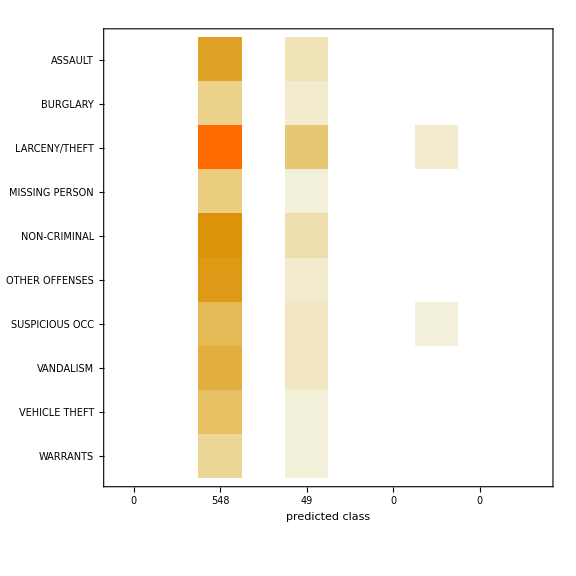

```mathematica
Show[cm["ConfusionMatrixPlot"],ImageSize->Large]
```

The results from this classifier show that it hugely overestimates the number of larceny/theft crimes, and the model could definitely could be improved upon.

#### Examining other Classification Methods

```mathematica
rs=RandomSample[reducedDs,500];     (* Take a smaller random sample of the top ten crimes. *)
train=GroupBy[Table[rs[i][["Category"]]->Values[rs[i][[features]]],{i,1,Round[Length[rs]*0.7]}],First->Last];
test=GroupBy[Table[rs[i][["Category"]]->Values[rs[i][[features]]],{i,Round[Length[rs]*0.7]+1,Round[Length[rs]]}],First->Last];
```

```mathematica
results=Dataset@GroupBy[Table[c1=Classify[train,Method->method,PerformanceGoal->"Quality"];
method->Dataset@ClassifierMeasurements[c1,test,"FScore"],{method,{"NeuralNetwork","LogisticRegression","SupportVectorMachine","RandomForest","NearestNeighbors"}}],First->Last];
```

```mathematica
Transpose[results]
```

Dataset[<>]

RandomForest is the most accurate classification method, with all of the other available methods just predicting “larceny/theft” cases.

## Conclusion

Mathematica contains some useful tools for data analysis, and the built-in information that it has access to such as geographical maps greatly simplifies tasks like plotting coordinates. The classification model fitted was not particularly accurate, and as an extension to this project, it could be useful to look at supplying more data to the Classifier function. We could also engineering some new features that would act as more accurate predictors.